∞

-π/4

{{-1+delta,1+delta},{{-1/(√2),1/(√2)},{1/(√2),1/(√2)}}}

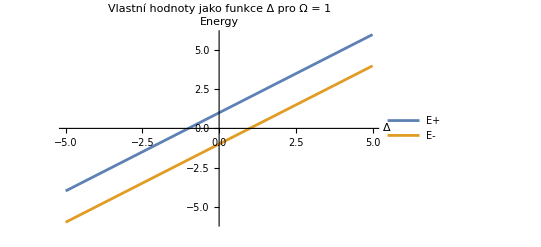

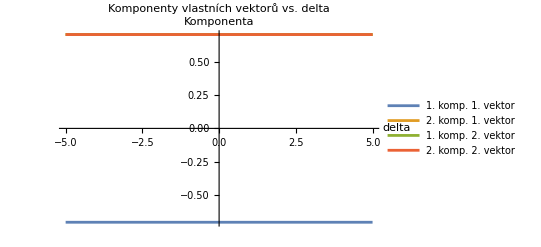

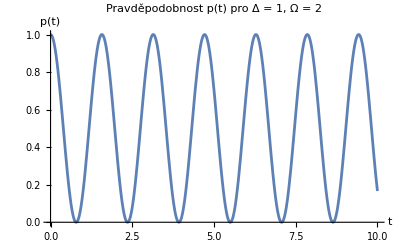

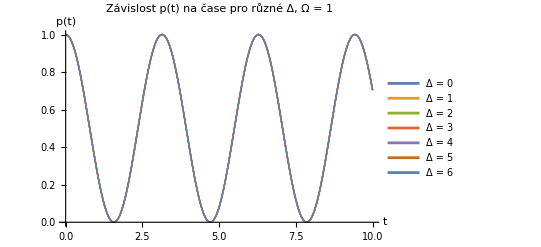

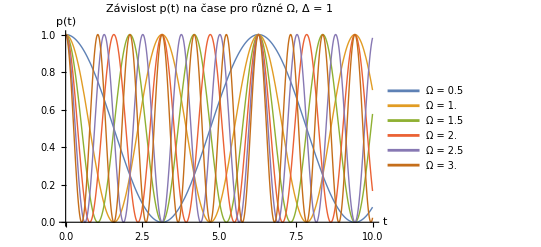

```mathematica
(* ===Úkol 1:Výpočet limity===*)Limit[(CubeRoot[Sin[x]+x^3]-x)/x^5,x->0]


(*Úkol 2:Výpočet určitého integrálu*)
Integrate[Log[x]/(x^2+1)^2,{x,0,Infinity}]


(* ===Úkol 3:Vlastní hodnoty a normované vektory Hamiltoniánu===*)H[delta_]:={{delta,1},{1,delta}};
{vals,vecs}=Eigensystem[H[delta]];
normalizedVecs=Normalize/@vecs;
{vals,normalizedVecs}



(* ===Úkol 4:Vykreslení vlastních hodnot jako funkce delta===*)
Plot[{delta+1,delta-1},{delta,-5,5},PlotLegends->{"E+","E-"},AxesLabel->{"Δ","Energy"},PlotLabel->"Vlastní hodnoty jako funkce Δ pro Ω = 1"]


(* ===Úkol 5:Komponenty vlastních vektorů===*)
normalizedVectors[delta_]:=Normalize/@Eigenvectors[H[delta]];
comp11[delta_]:=normalizedVectors[delta][[1,1]];
comp12[delta_]:=normalizedVectors[delta][[1,2]];
comp21[delta_]:=normalizedVectors[delta][[2,1]];
comp22[delta_]:=normalizedVectors[delta][[2,2]];
Plot[Evaluate@{comp11[delta],comp12[delta],comp21[delta],comp22[delta]},{delta,-5,5},PlotLegends->{"1. komp. 1. vektor","2. komp. 1. vektor","1. komp. 2. vektor","2. komp. 2. vektor"},PlotLabel->"Komponenty vlastních vektorů vs. delta",AxesLabel->{"delta","Komponenta"}]


(* ===Úkol 6:Časový vývoj kvantového systému===*)
H[delta_,omega_]:={{delta,omega},{omega,delta}};
psi0={1,0};
psi[delta_,omega_,t_]:=MatrixExp[-I H[delta,omega] t].psi0;
p[delta_,omega_,t_]:=Abs[Conjugate[psi0].psi[delta,omega,t]]^2;

(*Jedna křivka:Δ=1,Ω=2*)
Plot[p[1,2,t],{t,0,10},AxesLabel->{"t","p(t)"},PlotLabel->"Pravděpodobnost p(t) pro Δ = 1, Ω = 2"]

(*Více křivek pro různé Δ při konstantní Ω*)
Plot[Evaluate@Table[p[delta,1,t],{delta,0,6,1}],{t,0,10},PlotLegends->Placed[LineLegend[Table["Δ = "<>ToString[delta],{delta,0,6,1}]],Above],PlotStyle->Table[Directive[Thick,ColorData[97][i]],{i,6}],AxesLabel->{"t","p(t)"},PlotLabel->"Závislost p(t) na čase pro různé Δ, Ω = 1"]

(*Více křivek pro různé Ω při konstantní Δ*)
Plot[Evaluate@Table[p[1,omega,t],{omega,0.5,3,0.5}],{t,0,10},PlotLegends->Placed[LineLegend[Table["Ω = "<>ToString[omega],{omega,0.5,3,0.5}]],Above],PlotStyle->Table[Directive[Thick,ColorData[97][i]],{i,6}],AxesLabel->{"t","p(t)"},PlotLabel->"Závislost p(t) na čase pro různé Ω, Δ = 1"]
```